```mathematica
ω=2/(1+√5);
```

```mathematica
exp=2 ω^(2 q)(ρ/2)^((1-q) d)+ω^(3 q)ρ^(2 (1-q) d)-1;
```

```mathematica
exp/.d->1/(1-q)Log[ω^-q(√(1+ω^-q)-1)]/Log[ρ];
Limit[%,ρ->0]
```

0

```mathematica
num[qq_,ρρ_]:=(d/.FindRoot[(exp/.{q->qq,ρ->ρρ}),{d,0}]);
```

```mathematica
dth[qq_,ρρ_]:=1/(1-qq)Log[ω^-qq(√(1+ω^-qq)-1)]/Log[ρρ];
```

```mathematica
glue[l1_,l2_]:=MapThread[{#1,#2}&,{l1,l2}];
```

```mathematica
q0=0.;
rholist=Range[0.001,0.5,0.002];
thlist=dth[q0,#]&/@rholist;
numlist=num[q0,#]&/@rholist;
```

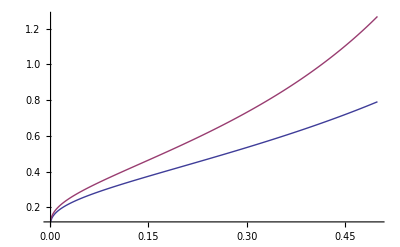

```mathematica
ListPlot[glue[rholist,#]&/@{numlist,thlist},PlotRange->All,Joined->True]
```